```mathematica
b[x_]:=4/x∑_(j=-100)^100 (1+(BesselY[j,x]/BesselJ[j,x])^2)^-1
```

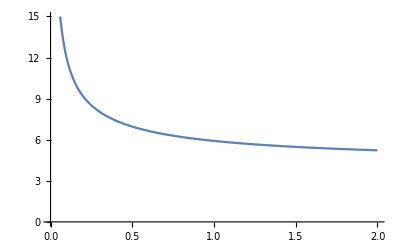

```mathematica
Plot[b[x],{x,0,2},PlotRange->{0,15}]
```